## 187Au

```mathematica
ClearAll["Global`*"]
```

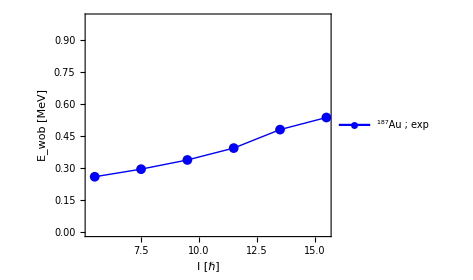

```mathematica
yrastEn=Sort[{5036.5,4259.6,3502.0,2796.2,2158.4,1591.2,1100.3,687.0,353.3,120.5}];
wob1En=Sort[{3013.7,2354.7,1739.3,1231.7,815.2,496.5}];
yrastSpin=Table[i/2,{i,9,45,4}];
wob1Spin=Table[i/2,{i,11,35,4}];
wobbling[yrast_,b1_,spins_]:=Table[{spins[[i]],b1[[i]]/1000-1/2(yrast[[i]]+yrast[[i+1]])/1000},{i,1,Length[b1]}];
data=wobbling[yrastEn,wob1En,wob1Spin];
fig=ListPlot[data,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,PlotStyle->{Thick,Blue},FrameStyle->Directive[Thick,Black],FrameLabel->{"I [ℏ]","E_wob [MeV]"},LabelStyle->{20,Bold,Black},PlotLegends->Placed[{Style[Row[{Superscript["","187"],"Au ; exp"}],30]},{0.4,0.85}],ImageSize->350,PlotRange->{Full,{0,1}}];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/187Au.pdf",fig];
Show[fig]
```